```mathematica
ClearAll["Global`*"]
```

## Initialization Values :

```mathematica
eq=Sqrt[(4*π)/137];
za=0.0067;zs=0.533;
Ba=1/3;
Qu=(2*eq)/3;Qd=-eq/3;Qs=-eq/3;
Su=0;Sd=0;Ss=-1;
xiu[xib_,xiq_,xis_]:=Ba*xib+Qu*xiq+Su*xis;
xid[xib_,xiq_,xis_]:=Ba*xib+Qd*xiq+Sd*xis;
xis[xib_,xiq_,xis_]:=Ba*xib+Qs*xiq+Ss*xis;
```

## Basic Integrals :

```mathematica
fu[x_,xib_,xiq_,xs_]:=1/(Exp[Sqrt[x^2+za^2]-(Ba*xib+Qu*xiq+Su*xs)]+1);
fd[x_,xib_,xiq_,xs_]:=1/(Exp[Sqrt[x^2+za^2]-(Ba*xib+Qd*xiq+Sd*xs)]+1);
fs[x_,xib_,xiq_,xs_]:=1/(Exp[Sqrt[x^2+zs^2]-(Ba*xib+Qs*xiq+Ss*xs)]+1);
afu[x_,xib_,xiq_,xs_]:=1/(Exp[Sqrt[x^2+za^2]+(Ba*xib+Qu*xiq+Su*xs)]+1);
afd[x_,xib_,xiq_,xs_]:=1/(Exp[Sqrt[x^2+za^2]+(Ba*xib+Qd*xiq+Sd*xs)]+1);
afs[x_,xib_,xiq_,xs_]:=1/(Exp[Sqrt[x^2+zs^2]+(Ba*xib+Qs*xiq+Ss*xs)]+1);

igpu[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=(T^(n+2)*da)/((2*q+1)!!)*(-1)^q/(2*π^2)*(Sqrt[x^2+za^2])^(n-2*q-1)*x^(2*q+2)*(fu[x,xib,xiq,xs]+afu[x,xib,xiq,xs]);
igpd[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=(T^(n+2)*da)/((2*q+1)!!)*(-1)^q/(2*π^2)*(Sqrt[x^2+za^2])^(n-2*q-1)*x^(2*q+2)*(fd[x,xib,xiq,xs]+afd[x,xib,xiq,xs]);
igps[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=(T^(n+2)*da)/((2*q+1)!!)*(-1)^q/(2*π^2)*(Sqrt[x^2+zs^2])^(n-2*q-1)*x^(2*q+2)*(fs[x,xib,xiq,xs]+afs[x,xib,xiq,xs]);
igmu[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=(T^(n+2)*da)/((2*q+1)!!)*(-1)^q/(2*π^2)*(Sqrt[x^2+za^2])^(n-2*q-1)*x^(2*q+2)*(fu[x,xib,xiq,xs]-afu[x,xib,xiq,xs]);
igmd[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=(T^(n+2)*da)/((2*q+1)!!)*(-1)^q/(2*π^2)*(Sqrt[x^2+za^2])^(n-2*q-1)*x^(2*q+2)*(fd[x,xib,xiq,xs]-afd[x,xib,xiq,xs]);
igms[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=(T^(n+2)*da)/((2*q+1)!!)*(-1)^q/(2*π^2)*(Sqrt[x^2+zs^2])^(n-2*q-1)*x^(2*q+2)*(fs[x,xib,xiq,xs]-afs[x,xib,xiq,xs]);


ipu[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=NIntegrate[igpu[x,n,q,T,xib,xiq,xs,da],{x,0,∞},PrecisionGoal->12,AccuracyGoal->14,WorkingPrecision->30];
ipd[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=NIntegrate[igpd[x,n,q,T,xib,xiq,xs,da],{x,0,∞},PrecisionGoal->12,AccuracyGoal->14,WorkingPrecision->30];
ips[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=NIntegrate[igps[x,n,q,T,xib,xiq,xs,da],{x,0,∞},PrecisionGoal->12,AccuracyGoal->14,WorkingPrecision->30];
imu[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=NIntegrate[igmu[x,n,q,T,xib,xiq,xs,da],{x,0,∞},PrecisionGoal->12,AccuracyGoal->14,WorkingPrecision->30];
imd[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=NIntegrate[igmd[x,n,q,T,xib,xiq,xs,da],{x,0,∞},PrecisionGoal->12,AccuracyGoal->14,WorkingPrecision->30];
ims[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=NIntegrate[igms[x,n,q,T,xib,xiq,xs,da],{x,0,∞},PrecisionGoal->12,AccuracyGoal->14,WorkingPrecision->30];


jpu[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=T*((n-2*q)ipu[n-1,q,T,xib,xiq,xs,da]-ipu[n-1,q-1,T,xib,xiq,xs,da]);
jpd[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=T*((n-2*q)ipd[n-1,q,T,xib,xiq,xs,da]-ipd[n-1,q-1,T,xib,xiq,xs,da]);
jps[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=T*((n-2*q)ips[n-1,q,T,xib,xiq,xs,da]-ips[n-1,q-1,T,xib,xiq,xs,da]);
jmu[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=T*((n-2*q)imu[n-1,q,T,xib,xiq,xs,da]-imu[n-1,q-1,T,xib,xiq,xs,da]);
jmd[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=T*((n-2*q)imd[n-1,q,T,xib,xiq,xs,da]-imd[n-1,q-1,T,xib,xiq,xs,da]);
jms[n_?NumericQ,q_?NumericQ,T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,da_?NumericQ]:=T*((n-2*q)ims[n-1,q,T,xib,xiq,xs,da]-ims[n-1,q-1,T,xib,xiq,xs,da]);
```

## Necessary Variables :

```mathematica
nu[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,Nf_?NumericQ]:=imu[1,0,T,xib,xiq,xs,Nf];
nd[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,Nf_?NumericQ]:=imd[1,0,T,xib,xiq,xs,Nf];
ns[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,Nf_?NumericQ]:=ims[1,0,T,xib,xiq,xs,Nf];
nB[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=Ba*imu[1,0,T,xib,xiq,xs,du]+Ba*imd[1,0,T,xib,xiq,xs,dd]+Ba*ims[1,0,T,xib,xiq,xs,ds];
nQ[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=Qu*imu[1,0,T,xib,xiq,xs,du]+Qd*imd[1,0,T,xib,xiq,xs,dd]+Qs*ims[1,0,T,xib,xiq,xs,ds];
nS[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=Su*imu[1,0,T,xib,xiq,xs,du]+Sd*imd[1,0,T,xib,xiq,xs,dd]+Ss*ims[1,0,T,xib,xiq,xs,ds];


et[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=ipu[2,0,T,xib,xiq,xs,du]+ipd[2,0,T,xib,xiq,xs,dd]+ips[2,0,T,xib,xiq,xs,ds]+(8*π^2*T^4)/15;
pt[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=-ipu[2,1,T,xib,xiq,xs,du]-ipd[2,1,T,xib,xiq,xs,dd]-ips[2,1,T,xib,xiq,xs,ds]+(8*π^2*T^4)/45;


bbb[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=-(Ba*Ba*(jpu[1,1,T,xib,xiq,xs,du]+jpd[1,1,T,xib,xiq,xs,dd]+jps[1,1,T,xib,xiq,xs,ds])+((nB[T,xib,xiq,xs,du,dd,ds])^2*T)/(et[T,xib,xiq,xs,du,dd,ds]+pt[T,xib,xiq,xs,du,dd,ds]));
bqq[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=-((Qu*Qu*jpu[1,1,T,xib,xiq,xs,du]+Qd*Qd*jpd[1,1,T,xib,xiq,xs,dd]+Qs*Qs*jps[1,1,T,xib,xiq,xs,ds])+((nQ[T,xib,xiq,xs,du,dd,ds])^2*T)/(et[T,xib,xiq,xs,du,dd,ds]+pt[T,xib,xiq,xs,du,dd,ds]));
bss[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=-((Su*Su*jpu[1,1,T,xib,xiq,xs,du]+Sd*Sd*jpd[1,1,T,xib,xiq,xs,dd]+Ss*Ss*jps[1,1,T,xib,xiq,xs,ds])+((nS[T,xib,xiq,xs,du,dd,ds])^2*T)/(et[T,xib,xiq,xs,du,dd,ds]+pt[T,xib,xiq,xs,du,dd,ds]));
bbq[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=-(Ba*(Qu*jpu[1,1,T,xib,xiq,xs,du]+Qd*jpd[1,1,T,xib,xiq,xs,dd]+Qs*jps[1,1,T,xib,xiq,xs,ds])+(nB[T,xib,xiq,xs,du,dd,ds]*nQ[T,xib,xiq,xs,du,dd,ds]*T)/(et[T,xib,xiq,xs,du,dd,ds]+pt[T,xib,xiq,xs,du,dd,ds]));
bbs[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=-(Ba*(Su*jpu[1,1,T,xib,xiq,xs,du]+Sd*jpd[1,1,T,xib,xiq,xs,dd]+Ss*jps[1,1,T,xib,xiq,xs,ds])+(nB[T,xib,xiq,xs,du,dd,ds]*nS[T,xib,xiq,xs,du,dd,ds]*T)/(et[T,xib,xiq,xs,du,dd,ds]+pt[T,xib,xiq,xs,du,dd,ds]));
bqs[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=-((Qu*Su*jpu[1,1,T,xib,xiq,xs,du]+Qd*Sd*jpd[1,1,T,xib,xiq,xs,dd]+Qs*Ss*jps[1,1,T,xib,xiq,xs,ds])+(nB[T,xib,xiq,xs,du,dd,ds]*nQ[T,xib,xiq,xs,du,dd,ds]*T)/(et[T,xib,xiq,xs,du,dd,ds]+pt[T,xib,xiq,xs,du,dd,ds]));


bpt[T_?NumericQ,xib_?NumericQ,xiq_?NumericQ,xs_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=(1/T)*(jpu[3,2,T,xib,xiq,xs,du]+jpd[3,2,T,xib,xiq,xs,dd]+jps[3,2,T,xib,xiq,xs,ds]+(32*T^5*π^2)/225);


Rbb[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=(bbb[T,b,q,s,du,dd,ds]*T)/bpt[T,b,q,s,du,dd,ds];
Rqq[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=(bqq[T,b,q,s,du,dd,ds]*T)/bpt[T,b,q,s,du,dd,ds];
Rss[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=(bss[T,b,q,s,du,dd,ds]*T)/bpt[T,b,q,s,du,dd,ds];
Rbq[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=(bbq[T,b,q,s,du,dd,ds]*T)/bpt[T,b,q,s,du,dd,ds];
Rbs[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=(bbs[T,b,q,s,du,dd,ds]*T)/bpt[T,b,q,s,du,dd,ds];
Rqs[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ,du_?NumericQ,dd_?NumericQ,ds_?NumericQ]:=(bqs[T,b,q,s,du,dd,ds]*T)/bpt[T,b,q,s,du,dd,ds];


RT1[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ]:=((et[T,b,q,s,6,0,0]+pt[T,b,q,s,6,0,0])/((b*nB[T,b,q,s,6,0,0]+q*nQ[T,b,q,s,6,0,0]+s*nS[T,b,q,s,6,0,0])*T*π))^2*(b^2*Rbb[T,b,q,s,6,0,0]+q^2*Rqq[T,b,q,s,6,0,0]+s^2*Rss[T,b,q,s,6,0,0]+2*b*q*Rbq[T,b,q,s,6,0,0]+2*b*s*Rbs[T,b,q,s,6,0,0]+2*q*s*Rqs[T,b,q,s,6,0,0])*((Ba*b+Qu*q+Su*s)^2);
RT2[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ]:=((et[T,b,q,s,6,6,0]+pt[T,b,q,s,6,6,0])/((b*nB[T,b,q,s,6,6,0]+q*nQ[T,b,q,s,6,6,0]+s*nS[T,b,q,s,6,6,0])*T*π))^2*(b^2*Rbb[T,b,q,s,6,6,0]+q^2*Rqq[T,b,q,s,6,6,0]+s^2*Rss[T,b,q,s,6,6,0]+2*b*q*Rbq[T,b,q,s,6,6,0]+2*b*s*Rbs[T,b,q,s,6,6,0]+2*q*s*Rqs[T,b,q,s,6,6,0])*(((Ba*b+Qu*q+Su*s)^4+(Ba*b+Qd*q+Sd*s)^4)/((Ba*b+Qu*q+Su*s)^2+(Ba*b+Qd*q+Sd*s)^2));
RT3[T_?NumericQ,b_?NumericQ,q_?NumericQ,s_?NumericQ]:=((et[T,b,q,s,6,6,6]+pt[T,b,q,s,6,6,6])/((b*nB[T,b,q,s,6,6,6]+q*nQ[T,b,q,s,6,6,6]+s*nS[T,b,q,s,6,6,6])*T*π))^2*(b^2*Rbb[T,b,q,s,6,6,6]+q^2*Rqq[T,b,q,s,6,6,6]+s^2*Rss[T,b,q,s,6,6,6]+2*b*q*Rbq[T,b,q,s,6,6,6]+2*b*s*Rbs[T,b,q,s,6,6,6]+2*q*s*Rqs[T,b,q,s,6,6,6])*(((Ba*b+Qu*q+Su*s)^4+(Ba*b+Qd*q+Sd*s)^4+(Ba*b+Qs*q+Ss*s)^4)/((Ba*b+Qu*q+Su*s)^2+(Ba*b+Qd*q+Sd*s)^2+(Ba*b+Qs*q+Ss*s)^2));
```

```mathematica
Rbq[0.15,0.0,0.0,0.0,6,6,6]
```

0.000264618

```mathematica
RT1[0.15,0.1,0.0,0.0]
RT2[0.15,0.1,0.0,0.0]
RT3[0.15,0.1,0.0,0.0]
```

1.96298

1.37033

1.16415

## Plots :

```mathematica
LogLinearPlot[{RT1[0.15,a,0,0],Labeled[ConditionalExpression[53/27,0.01<a<2],"Nf=1",{0.018,1.97}],(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)Labeled[ConditionalExpression[5/3,20<a<100],"5/3",{85,1.6}]},{a,0.01,100},Frame->True,PlotStyle->{Directive[Blue],Directive[White,Dotted],(*Directive[Orange,Dashed],Directive[Blue,Opacity[0]],Directive[Blue,Opacity[0]],*)Directive[Red,Dashed]},PlotRange->{{0.01,100},{1.5,2.1}}]
```

-Graphics-

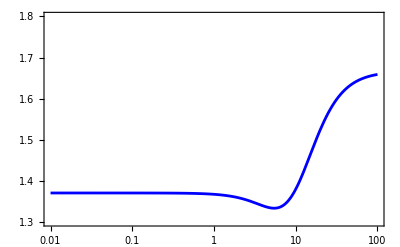

```mathematica
LogLinearPlot[{RT2[0.15,a,0,0]/2}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.01,100},Frame->True,PlotStyle->{Directive[Blue](*,Directive[White,Dotted],Directive[Red,Dashed]*)},PlotRange->{{0.01,100},{1.3,1.8}}]
```

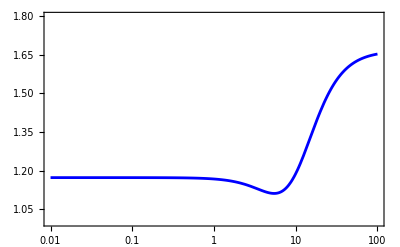

```mathematica
LogLinearPlot[{RT3[0.15,a,0,0]/3}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.01,100},Frame->True,PlotStyle->{Directive[Blue](*,Directive[White,Dotted],Directive[Red,Dashed]*)},PlotRange->{{0.01,100},{1.0,1.8}}]
```

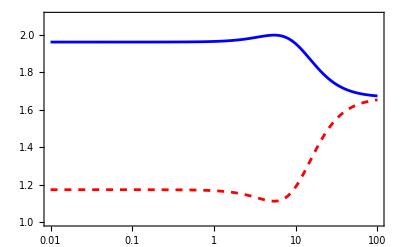

```mathematica
LogLinearPlot[{RT1[0.15,a,0,0],RT2[0.15,a,0,0]/2,RT3[0.15,a,0,0]/3}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.01,100},Frame->True,PlotStyle->{Directive[Blue],Directive[White,Dotted],Directive[Red,Dashed]},PlotRange->{{0.01,100},{1.0,2.1}}]
```

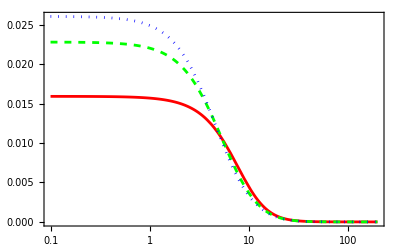

```mathematica
LogLinearPlot[{Rbb[0.15,a,0,0,6,0,0],Rbb[0.15,a,0,0,6,6,0],Rbb[0.15,a,0,0,6,6,6]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{Directive[Red],Directive[Green,Darker,Dashed],Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

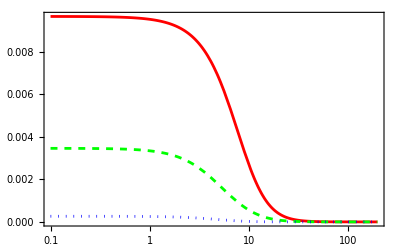

```mathematica
LogLinearPlot[{Rbq[0.15,a,0,0,6,0,0],Rbq[0.15,a,0,0,6,6,0],Rbq[0.15,a,0,0,6,6,6]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{Directive[Red],Directive[Green,Darker,Dashed],Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

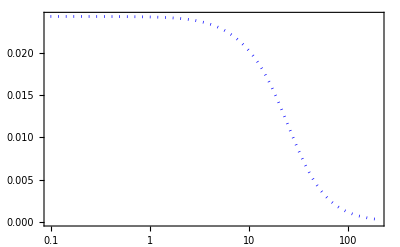

```mathematica
LogLinearPlot[{-Rbs[0.15,0,a,0,6,6,6]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{(*Directive[Red],Directive[Green,Darker,Dashed],*)Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

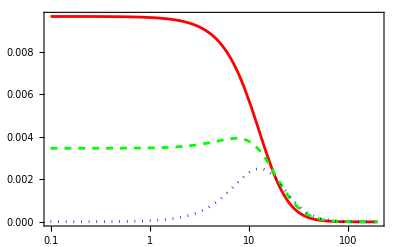

```mathematica
LogLinearPlot[{Rbq[0.15,0,a,0,6,0,0],Rbq[0.15,0,a,0,6,6,0],Rbq[0.15,0,a,0,6,6,6]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{Directive[Red],Directive[Green,Darker,Dashed],Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

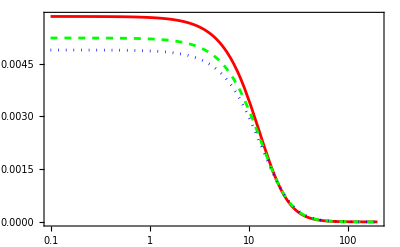

```mathematica
LogLinearPlot[{Rqq[0.15,0,a,0,6,0,0],Rqq[0.15,0,a,0,6,6,0],Rqq[0.15,0,a,0,6,6,6]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{Directive[Red],Directive[Green,Darker,Dashed],Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

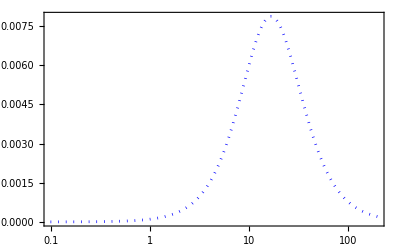

```mathematica
LogLinearPlot[{-Rqs[0.15,0,a,0,6,0,0]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{Directive[Red],Directive[Green,Darker,Dashed],Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

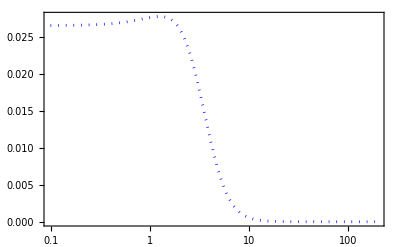

```mathematica
LogLinearPlot[{-Rbs[0.15,0,0,a,6,6,6]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{Directive[Red],Directive[Green,Darker,Dashed],Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

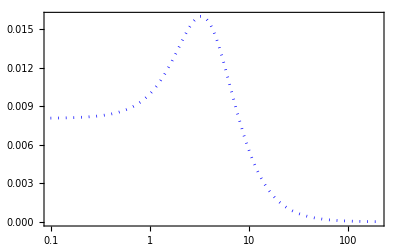

```mathematica
LogLinearPlot[{Rqs[0.15,0,0,a,6,6,6]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{Directive[Red],Directive[Green,Darker,Dashed],Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

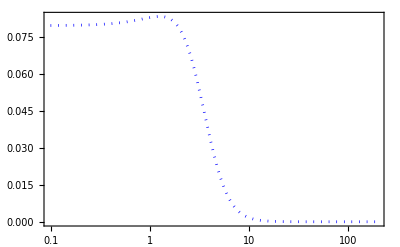

```mathematica
LogLinearPlot[{Rss[0.15,0,0,a,6,6,6]}(*,Labeled[ConditionalExpression[37/27,0.01<a<2],"Nf=2",{0.018,1.45}],*)(*Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2",{0.018,1.45}],Labeled[ConditionalExpression[5/3,5<a<80],"Nf=2+1",{0.018,1.15}],*)(*Labeled[ConditionalExpression[5/3,80<a<100],"5/3",{85,1.6}]}*),{a,0.1,200},Frame->True,PlotStyle->{Directive[Red],Directive[Green,Darker,Dashed],Directive[Blue,Dotted]}(*,PlotRange->{{0.1,45},{1.0,2.1}}*)]
```

## Data Export :

```mathematica
LaunchKernels[];
DistributeDefinitions[(*mu,md,ms,*)
eq,za,zs,
Ba,Qu,Qd,Qs,Su,Sd,Ss,
xiu,xid,xis,
fu,afu,fd,afd,fs,afs,(*fut,afut,fdt,afdt,fst,afst,*)
igpu,igmu,igpd,igmd,igps,igms,
ipu,imu,ipd,imd,ips,ims,
jpu,jmu,jpd,jmd,jps,jms,
nu,nd,ns,nB,nQ,nS,et,pt,
bbb,bqq,bss,bbq,bbs,bqs,bpt,
Rbb,Rqq,Rss,Rbq,Rbs,Rqs,
RT1,RT2,RT3];
```

### Table Generation :

```mathematica
RbbB=ParallelTable[{i,1.Rbb[1,i,0,0,6,0,0],1. Rbb[1,i,0,0,6,6,0],1. Rbb[1,i,0,0,6,6,6]},{i,0.1,100,0.1}]//Quiet;
RbqB=ParallelTable[{i,1.Rbq[1,i,0,0,6,0,0],1. Rbq[1,i,0,0,6,6,0],1. Rbq[1,i,0,0,6,6,6]},{i,0.1,100,0.1}]//Quiet;
RbsB=ParallelTable[{i,(*1.Rbs[1,i,0,0,6,0,0],1. Rbs[1,i,0,0,6,6,0],*)1. Rbs[1,i,0,0,6,6,6]},{i,0.1,100,0.1}]//Quiet;
RbqQ=ParallelTable[{i,1.Rbq[1,0,i,0,6,0,0],1. Rbq[1,0,i,0,6,6,0],1. Rbq[1,0,i,0,6,6,6]},{i,0.1,100,0.1}]//Quiet;
RqqQ=ParallelTable[{i,1.Rqq[1,0,i,0,6,0,0],1. Rqq[1,0,i,0,6,6,0],1. Rqq[1,0,i,0,6,6,6]},{i,0.1,100,0.1}]//Quiet;
RqsQ=ParallelTable[{i,(*1.Rqs[1,0,i,0,6,0,0],1. Rqs[1,0,i,0,6,6,0],*)1. Rqs[1,0,i,0,6,6,6]},{i,0.1,100,0.1}]//Quiet;
RbsS=ParallelTable[{i,(*1.Rbs[1,0,0,i,6,0,0],1. Rbs[1,0,0,i,6,6,0],*)1. Rbs[1,0,0,i,6,6,6]},{i,0.1,100,0.1}]//Quiet;
RqsS=ParallelTable[{i,(*1.Rqs[1,0,0,i,6,0,0],1. Rqs[1,0,0,i,6,6,0],*)1. Rqs[1,0,0,i,6,6,6]},{i,0.1,100,0.1}]//Quiet;
RssS=ParallelTable[{i,(*1.Rss[1,0,0,i,6,0,0],1. Rss[1,0,0,i,6,6,0],*)1. Rss[1,0,0,i,6,6,6]},{i,0.1,100,0.1}]//Quiet;
```

```mathematica
RkT1B=ParallelTable[{i,1.RT1[1,i,0,0]},{i,0.05,140,0.05}]//Quiet;
```

```mathematica
RkT2B=ParallelTable[{i,1. RT2[1,i,0,0]},{i,0.05,140,0.05}]//Quiet;
```

```mathematica
RkT3B=ParallelTable[{i,1. RT3[1,i,0,0]},{i,0.05,140,0.05}]//Quiet;
```

#### Exporting the Data

```mathematica
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RbbB.csv",RbbB,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RbqB.csv",RbqB,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RbsB.csv",RbsB,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RbqQ.csv",RbqQ,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RqqQ.csv",RqqQ,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RqsQ.csv",RqsQ,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RsbS.csv",RbsS,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RsqS.csv",RqsS,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RssS.csv",RssS,"Table"];
```

```mathematica
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RkT1B.csv",RkT1B,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RkT2B.csv",RkT2B,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RkT3B.csv",RkT3B,"Table"];
```